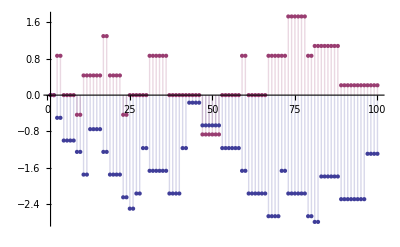

{{1,0.,0.},{2,0.,0.},{3,-0.5,0.866025},{4,0.,0.},{5,-0.5,-0.866025},{6,0.,0.},{7,0.,0.},{8,0.,0.},{9,-0.25,-0.433013},{10,0.,0.},{11,-0.5,0.866025},{12,0.,0.},{13,1.,0.},{14,0.,0.},{15,0.,0.},{16,0.,0.},{17,-0.5,0.866025},{18,0.,0.},{19,-0.5,-0.866025},{20,0.,0.},{21,0.,0.},{22,0.,0.},{23,-0.5,-0.866025},{24,0.,0.},{25,-0.25,0.433013},{26,0.,0.},{27,0.333333,0.},{28,0.,0.},{29,1.,0.},{30,0.,0.},{31,-0.5,0.866025},{32,0.,0.},{33,0.,0.},{34,0.,0.},{35,0.,0.},{36,0.,0.},{37,-0.5,-0.866025},{38,0.,0.},{39,0.,0.},{40,0.,0.}}

```mathematica
Clear[f]
a[n_] := DirichletCharacter[14,3,n]
f[n_,k_] := f[n,k]=Sum[ a[j]f[Floor[n/j],k-1],{j,2,n}]
f[n_, 0] := UnitStep[n-1]
lf[n_] := Sum[ (-1)^(k+1)/k f[n,k],{k,1,Log2@n}]
DiscretePlot[{ Re[lf[n]], Im[lf[n]]},{n,1,100}]
Table[{ n,N@Re[lf[n]-lf[n-1]],N@Im[lf[n]-lf[n-1]]},{n,1,40}]
```

```mathematica
N@lf[100]
```

-1.29167+0.216506 ⅈ

```mathematica
Sum[ N@(a[j] MangoldtLambda[j]/Log[j]),{j,2,100}]
```

-1.29167+0.216506 ⅈ